```mathematica
"Multipole Double U - Adjacent Inlet Pipes"
```

```mathematica
temp:=50(*in celcius*);
tempr:=50+273.15
```

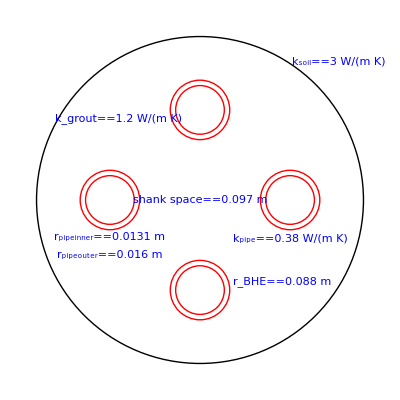

```mathematica
rhof=ThermodynamicData["Water","Density",{"Temperature"-> Quantity[tempr,"Kelvins"]}](*988.04 for 50°C*) (*fluid density[kg/m^3]*); 
mu=ThermodynamicData["Water","Viscosity",{"Temperature"-> Quantity[tempr,"Kelvins"]}](*0.0005465 for 50°C*)(*dynamic viscosity [Pa.s]*); 
cpf0=ThermodynamicData["Water","IsobaricHeatCapacity",{"Temperature"-> Quantity[tempr,"Kelvins"]}](*4182*) (*fluid specific heat capacity [J/kgK]*); 
cpf=UnitConvert[cpf0]/."KelvinsDifference"->"Kelvins";
kfluid0=ThermodynamicData["Water","ThermalConductivity",{"Temperature"-> Quantity[tempr,"Kelvins"]}](*0.64*) (*fluid thermal conductivity [W/(m.K)]*); 
kfluid=UnitConvert[kfluid0]/."KelvinsDifference"->"Kelvins";
Qi=Quantity[ 2*0.000266,("Meters"^3/"Seconds")] (*flow-rate[m^3/s]*); 
rpi=Quantity[0.0131,"Meters"] (*inner radius[m]*); 
kpipe=Quantity[0.38,("Watts"/("Meters"*"Kelvins"))] (*pipe thermal conductivity [W/(m.K)]*); 
rpo=Quantity[0.016,"Meters"] (*outer radius of pipe [m]*); 
kgrout=Quantity[1.2,("Watts"/("Meters"*"Kelvins"))] (*grout thermal conductivity [W/(m.K)]*); 
ss=Quantity[0.097,"Meters"] (*shank space [m]*); 
rb=Quantity[0.088,"Meters"](*borehole radius [m]*); 
ks=Quantity[3,("Watts"/("Meters"*"Kelvins"))](*ground thermal conductivity [W/(m.K)]*);
Hb=Quantity[50,"Meters"] (*Borehole depth [m]*);
rb1=QuantityMagnitude[rb];ss1=QuantityMagnitude[ss];rpo1=QuantityMagnitude[rpo];rpi1=QuantityMagnitude[rpi];rb1=QuantityMagnitude[rb];

Graphics[{Circle[{0,0},rb1],{Red,Circle[{-ss1/2,0},rpo1],Circle[{ss1/2,0},rpo1],Circle[{ss1/2,0},rpi1],Circle[{-ss1/2,0},rpi1]},{Red,Circle[{0,-ss1/2},rpo1],Circle[{0,ss1/2},rpo1],Circle[{0,ss1/2},rpi1],Circle[{0,-ss1/2},rpi1]},{Blue,Inset[Subscript[k, grout]==kgrout ,{-rb1/2,rb1/2}],Inset[Subscript[k, soil]==ks,{rb1*0.85,rb1*0.85}],Inset[Subscript[k, pipe]==kpipe ,{ss1/2,-rpo1*1.3}],Inset[Subscript[r, pipeinner]==rpi,{-ss1/2,-rpi1*1.5}],Inset[Subscript[r, pipeouter]==rpo,{-ss1/2,-rpi1*1.5-0.01}],Inset[shank space==ss,{0,0}],Inset[Subscript[r, BHE]==rb,{rb1/2,-rb1/2}]}}]
```

```mathematica
If[ss/2+rpo>rb,Style[Red]->"out of range","in the range"]
Vfluid=Qi/(π*rpi^2);
θ1=ss/(2*rb);
θ2=rb/rpo;
θ3=rpo/ss;
σ1=(kgrout-ks)/(kgrout+ks);
Rpc=1/(2*π*kpipe)*Log[rpo/rpi];
Re1=(rhof*Vfluid*2*rpi)/mu;
Pr=(cpf*mu)/kfluid;
ff=(0.79*Log[Re1]-1.64)^-2;
NUpi=((ff/8)*(Re1-1000)*Pr)/(1+12.7*(ff/8)^(1/2)*(Pr^(2/3)-1)) ; 
hpi=(NUpi*kfluid)/(2*rpi) ; 
Rpic=1/(2*π*rpi*hpi) ; 
Rp=Rpc+Rpic;
Beta1=2*π*kgrout*Rp;

Rb2U0=Rp/4+1/(8*π*kgrout)*(Log[rb^4/(4*rpo*(ss/2)^3)]+σ1*Log[rb^8/(rb^8-(ss/2)^8)]);
pbc=rpo^2/(4*(ss/2)^2);
pc=(ss/2)^2/((rb^8-(ss/2)^8)^(1/4));
pb=rb^2/((rb^8-(ss/2)^8)^(1/4));
b1=(1-Beta1)/(1+Beta1);
Rb2U1=Rb2U0-1/(8*π*kgrout)*(b1*pbc*(3-8*σ1*pc^4)^2)/(1+b1*pbc*(5+64*σ1*pc^4*pb^4));

Ra2U0=2*Rp+1/(π*kgrout)*(Log[(2*(ss/2))/rpo]+σ1*Log[(rb^2+(ss/2)^2)/(rb^2-(ss/2)^2)]);

V1=1-8*σ1*pb*pc^3;
V2=3+8*σ1*pc*pb^3;
M11=1+16*b1*σ1*pbc*(3*pc^3*pb^5+pb*pc^7);
M21=b1*pbc;
M12=-M21;
M22=-1-16*b1*σ1*pbc*(3*pc^5*pb^3+pc*pb^7);
Ra2U1=Ra2U0+1/(π*kgrout)*(b1*pbc)/2*(V2^2*M11-2*V1*V2*M21-V1^2*M22)/(M11*M22+M21^2);

Rv=Hb/(rhof*cpf*Qi);
Rbstar=Rb2U1+Rv^2/(3*Ra2U1);
Rbstar;
UnitConvert[Rbstar,("Kelvins"*"Meters"/"Watts")]
```

in the range

0.0897531 m K/W

```mathematica
Rbstar;
UnitConvert[Rbstar,("Kelvins"*"Meters"/"Watts")]
```

0.0897531 m K/W

```mathematica
Subscript[T̄, f]-Subscript[T̄, b,av]=Subscript[q̄, b].Subscript[R, b]^(*1U)
```

```mathematica
Subscript[T̄, f]: single mean of borehole entering  and exiting fluid temperatures °C
```

```mathematica
Subscript[T̄, b,av]: average borehole wall temperature around the borehole periphery over the borehole depth °C
```

```mathematica
Subscript[q̄, b]:mean heat flux over the borehole depth
```

```mathematica
Rbstar[988.04,0.000266,0.0131,0.0005465,4182,0.64,0.38,0.016,1.2,0.097,0.088,3,50]
```

0.147144